## Harvest model with Type III response - stationary simulation

## Setup and Universal Parameters

```mathematica
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_16/fold_harvest/figures"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* get package for user-defined functions *)
Get["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Mathematica/packages/my_functions/spectral_functions.wl"];
```

```mathematica
(* Universal simulation parameters *)
dt=0.1; (* time step for stochastic simulation *)
dt2 = 1; (* time separation for indicator calculation - increase to speed up computation *)
tmax=400 ; (* max time in simulation *)
numSims=100; (* number of realisations to average over *)

(* options for EWS calculation *)
detrendOp=1; (* 1 for yes, 0 for no *)
bandWidth=0.2; (* for Gaussian filtering (as a percentage) *)
rollWindow=0.25;(* for indicator calculation *)

(* hamming window size and length *)
hamLength=40; 
hamOffset=20; 


(* lag autocorrelation *)
numComps=tmax/dt+1; (* number of components in simulation *)
tauVals={1,2};

psdTime=250;(* time which psd computed *)

(* Figure display parameters *)
aHeadSize=0.03;
{padLeft,padRight,padBottom,padTop}={60,50,20,20};  (* image padding *)
indexPos=Scaled[{0.065,1.10}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos={0.035,0.86} ;(* panel letter label *)
```

## Model Analysis

Use bistable harvesting model : dx/dt = rx(1-x) - hx^2/(s^2 +x^2)

```mathematica
(* Clear variable names *)
Clear[f,x,r,h,s]
$Assumptions={x,r,a,s}∈Reals;
```

```mathematica
(* Dynamic equations *)
f[x_]:=r x(1-x) - h x^2/(s^2+x^2);
```

```mathematica
f[x]
```

r (1-x) x-(h x^2)/(s^2+x^2)

```mathematica
(* Parameter values *)
r=1;
s=0.1;
```

```mathematica
(* Find equilibiria *)
equi=Solve[f[x]==0,x]//Quiet;
```

```mathematica
equi/.{h->0.1}
```

{{x→0.},{x→0.0555458+0.0903572 ⅈ},{x→0.888908+0. ⅈ},{x→0.0555458-0.0903572 ⅈ}}

```mathematica
(* Initial stable equilibrium *)
equiInit=Re[x/.equi[[3]]];

(* Bifurcation point *)
{xbif,hbif}=Re[{x,h}/.Solve[f[x]==0&&f'[x]==0][[3]]]//Quiet
```

{0.478128,0.260437}

```mathematica
(* Eigenvalue at equilibrium point *)
Clear[λ]
λ[a_]=D[f[x],x]/.{x->equiInit};
```

```mathematica
(* Phase portrait, hval control parameter *)
Manipulate[
Plot[f[x]/.{r->rval,h->hval,s->sval},{x,0,1},
PlotRange->{-0.2,0.2},
AxesLabel->{"x","f(x)"},
LabelStyle->TMBFS12],
{{rval,1},0.5,1.5},{{hval,0},0,0.4},{{sval,0.1},0.05,0.3}];
```

## Stochastic Simulation

Stochastic model 
dX = rX(1-X) -hX^2/(s^2+X^2)

### Key parameters

```mathematica
a1=0.02;(* noise intensity *)
r=1; (* model parameteres *)
s=0.1;
hl=0.15; (* min value of control parameter *)
hh=0.15; (* max value of control parameter *)
x0=equiInit/.h->hl; (* initial condition *)
seed=10; (* seed number *)

(* lag autocorrelation *)
numComps=tmax/dt+1;
tauVals={1,2};
```

### Model Dynamics

```mathematica
Clear[f]
f[x_,h_]:=r x(1-x)-h x^2/(s^2+x^2);
```

### Stochastic Simulation

```mathematica
(* clear function labels *)
Clear[stochProc,stochSol,stochData]
```

```mathematica
(* evolution of control param - harvesting rate *)
Clear[h,t]
h[t_]:=((hh-hl)/tmax) t +hl
```

```mathematica
(* number of components in simulation *)
nComps=Floor[tmax/dt]+1;
```

```mathematica
(* array for output time-series *)
x=ConstantArray[0,{numSims,nComps}];
t=Range[0,tmax,dt];
```

```mathematica
(* intitial condition *)
x[[;;,1]]=x0;
```

```mathematica
(* noise values *)
noiseVals=RandomVariate[NormalDistribution[0,1],{numSims,nComps}];
```

```mathematica
(* set up counter *)
For[j=1,j≤numSims,j++,
For[i=1,i≤nComps-1,i++,
(* update state variable *)
x[[j,i+1]]=x[[j,i]]+f[x[[j,i]],h[t[[i]]]]dt+a1*Sqrt[dt]*noiseVals[[j,i]];
(* make sure state variable stays above x=0 *)
If[x[[j,i+1]]≤0,x[[j,i+1]]=0];
]
]
```

```mathematica
(* dimensions of xVals - (num realisations, tstep)  *)
x//Dimensions
```

{100,4001}

```mathematica
(* assign *)
tValsFull=t;
xValsFull=x;
```

### Filter time-series to improve computation time

```mathematica
(* Filter time-series seperation of dt2 to make analysis computationally feasible *)
tVals=Take[tValsFull,{1,Length[tValsFull],dt2/dt}];
xVals=Take[xValsFull,All,{1,Length[tValsFull],dt2/dt}];
```

### Single realisation plots

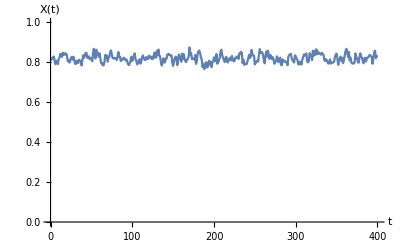

```mathematica
(* make plot of single realisation in x *)
plotX=ListPlot[{tVals,xVals[[2]]}ᵀ,
Joined->True,
ImageSize->400,
LabelStyle->14,
AxesLabel->{"t","X(t)"},
PlotRange->{0,1}]
```

## Traditional EWS

### Detrend - fit Gaussian

```mathematica
(* work with data only up to bifurcation (tcrit) *)
tcrit=339.805 (* same as for transient investigation *)
idxCrit=FirstPosition[tVals,t_/;t≥tcrit][[1]]-1;
tValsShort=tVals[[1;;idxCrit]];
```

339.805

```mathematica
dataFitX=If[detrendOp==1,
Table[GaussianFilter[xVals[[i,1;;idxCrit]],Length[tValsShort]*bandWidth],{i,1,numSims}],
ConstantArray[0,{numSims,idxCrit}]];
```

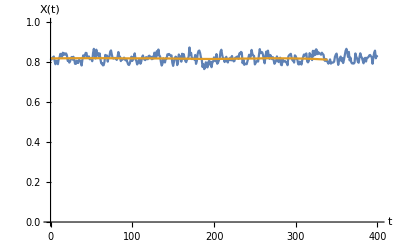

```mathematica
(* plot of a single X realisation fitted *)
fitPlotX=ListPlot[{{tVals,xVals[[2]]}ᵀ,{tValsShort,dataFitX[[2]]}ᵀ},
Joined->True,
ImageSize->400,
LabelStyle->14,
AxesLabel->{"t","X(t)"},
PlotRange->{{0,tmax},{0,1}}]
```

### Residuals

```mathematica
residualsX=xVals[[;;,1;;idxCrit]]-dataFitX;
residualsX//Dimensions
```

{100,340}

```mathematica
(* plot of a single realisation *)
residPlotX=ListPlot[{tValsShort,residualsX[[1]]}ᵀ,
Joined->True,
Filling->Axis,
AxesLabel->{"t","Res"},
LabelStyle->14,
ImageSize->400,
PlotRange->{{0,tmax},All}];
```

### Variation of Residuals

```mathematica
(* number of components in rolling window *)
windowComps=Floor[rollWindow*Length[tVals]];
```

```mathematica
(* compute variance of residuals - has form [v1;v2;v3;...;vn] *)
varSeriesX=Table[MovingMap[Variance,residualsX[[i]],windowComps],{i,1,numSims}];
varSeriesX//Dimensions
```

{100,240}

```mathematica
(* average over simulations *)
meanVarSeriesX=Mean[varSeriesX];
devVarSeriesX=StandardDeviation[varSeriesX];
```

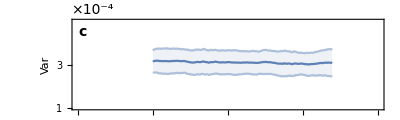

```mathematica
varAvPlotX=ListPlot[{{tValsShort[[windowComps+1;;]],meanVarSeriesX}ᵀ,
{tValsShort[[windowComps+1;;]],meanVarSeriesX+devVarSeriesX}ᵀ,
{tValsShort[[windowComps+1;;]],meanVarSeriesX-devVarSeriesX}ᵀ},
Joined->True,
PlotStyle->{TMBcolours⟦1⟧,Lighter[TMBcolours⟦1⟧,0.5],Lighter[TMBcolours⟦1⟧,0.5]},
Filling->{{2->{1}},{3->{1}}},
LabelStyle->14,
Frame->True,
PlotRange->{{0,tmax},{0.0001,0.0005}},
FrameLabel->{{"Var",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
FrameTicks->{{{{0.0001,1},{0.0002,2},{0.0003,3},{0.0004,4}},Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0}],Scaled[{0,arHeight},{windowComps*dt2,0}]}],
Text[Style["×10^-4",14],indexPos],
Text[Style["c",14,Bold],Scaled[labelLetterPos]]}]
```

### Autocorrelation of Residuals at various lags

```mathematica
(* form [a1;a2;,,,;an] *)
acSeriesX=Table[MovingMap[CorrelationFunction[#,tauVals[[j]]]&,residualsX[[i]],windowComps],{i,1,numSims},{j,1,Length[tauVals]}];  
acSeriesX//Dimensions
(* sim number, lag number, time value *)
```

{100,2,240}

```mathematica
(* line legend *)
legend=LineLegend[TMBcolours[[1;;3]],Table["τ="<>ToString[tauVals[[j]]],{j,1,Length[tauVals]}]];
```

```mathematica
(* average over simulations *)
meanAcSeriesX=Table[Mean[acSeriesX[[;;,j]]],{j,1,Length[tauVals]}];

(* deviation over simulations *)
devAcSeriesX=If[numSims>1,Table[StandardDeviation[acSeriesX[[;;,j]]],{j,1,Length[tauVals]}],
ConstantArray[0,Length[meanAcSeriesX]]];
```

```mathematica
(* ac plot for each lag in x *)
Clear[acAvPlotXfun];
acAvPlotXfun[j_]:=ListPlot[{
{tValsShort[[windowComps+1;;]],meanAcSeriesX[[j]]}ᵀ,
{tValsShort[[windowComps+1;;]],meanAcSeriesX[[j]]+devAcSeriesX[[j]]}ᵀ,
{tValsShort[[windowComps+1;;]],meanAcSeriesX[[j]]-devAcSeriesX[[j]]}ᵀ},
Joined->True,
PlotStyle->{TMBcolours[[j]],Lighter[TMBcolours[[j]],0.5],Lighter[TMBcolours[[j]],0.5]},
Filling->{{2->{1}},{3->{1}}},
LabelStyle->14,
Frame->True,
FrameLabel->{{"AC",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
PlotRange->{{0,tmax},{0,1}},
PlotRangeClipping->False,
PlotLegends->If[j==1,Placed[legend,{0.15,0.7}],None]];
```

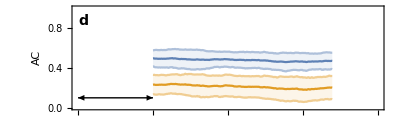

```mathematica
acAvPlotX=Show[Table[acAvPlotXfun[i],{i,1,Length[tauVals]}],
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0.1}],Scaled[{0,arHeight},{windowComps*dt2,0.1}]}],
Text[Style["",14],Scaled[{1.08,-0.05}]],
Text[Style["d",14,Bold],Scaled[labelLetterPos]]}]
```

## Power Spectrum EWS

### Compute power spectrum over rolling window

```mathematica
(*(* evaluate power spectrum of residuals in rolling window *)
pSpecSeriesX=Table[MovingMap[TBPowerSpecWelch[{#,dt2,hamLength,hamOffset}]&,residualsX[[i]],windowComps],{i,1,numSims}];*)
```

```mathematica
(*
(* export power spec data for one realisation *)
Export["../data_export/data_psd_stat.mat",pSpecSeriesX[[2]]];*)
```

```mathematica
(*(* flatten data to export it *)
pSpecSeriesFlat=Table[Flatten[pSpecSeriesX[[i,j]]],{i,1,numSims},{j,1,Dimensions[pSpecSeriesX][[2]]}];*)
```

```mathematica
(*pSpecSeriesFlat//Dimensions*)
```

```mathematica
(*(* export the power spectrum data *)
Export["../data_export/data_psd_stat.mat",pSpecSeriesFlat];*)
```

```mathematica
(* import power spec data *)
pSpecSeriesFlat=Import["../data_export/data_psd_stat.mat"];
```

```mathematica
pSpecSeriesFlat//Dimensions
```

{100,240,82}

```mathematica
(* recover original pspec form *)
pSpecSeriesX=Table[Partition[pSpecSeriesFlat[[i,j]],Dimensions[pSpecSeriesFlat][[3]]/2],{i,1,Dimensions[pSpecSeriesFlat][[1]]},{j,1,Dimensions[pSpecSeriesFlat][[2]]}];
```

```mathematica
pSpecSeriesX//Dimensions
```

{100,240,2,41}

```mathematica
(* frequncy values of power spectra *)
ωVals=pSpecSeriesX[[1,1,1]];
```

```mathematica
(* Find average power spectrum at time psdTime *)
windowComps=100;
meanPsdX=Mean[pSpecSeriesX[[;;,psdTime/dt2-windowComps,2]]];

devPsdX=StandardDeviation[pSpecSeriesX[[;;,psdTime/dt2-windowComps,2]]];
```

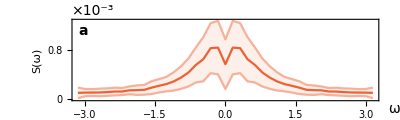

```mathematica
psdAvHopfX=ListPlot[{{ωVals,meanPsdX}//Transpose,
{ωVals,meanPsdX+devPsdX}//Transpose,
{ωVals,meanPsdX-devPsdX}//Transpose},
Joined->True,
Frame->True,
Filling->{{2->{1}},{3->{1}}},
LabelStyle->14,
PlotRange->{{-Pi,Pi},{0,All}},
PlotStyle->{TMBcolours⟦4⟧,Lighter[TMBcolours⟦4⟧,0.5],Lighter[TMBcolours⟦4⟧,0.5]},
FrameLabel->{{"S(ω)",""},{"",""}},
FrameTicks->{{{{0,0},{0.0004,0.4},{0.0008,0.8},{0.0012,1.2}},Automatic},{Automatic,Automatic}},
PlotRangeClipping->False,
Epilog->{Text[Style["×10^-3",14],indexPos],
Text[Style["ω",14],labelPos],
Text[Style["a",14,Bold],Scaled[labelLetterPos]]},
ImageSize->400,
AspectRatio->0.3,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}]
```

### Individual realisations

```mathematica
pSpecSeriesX//Dimensions
```

{100,240,2,41}

```mathematica
pSpec=pSpecSeriesX[[1,190]];
```

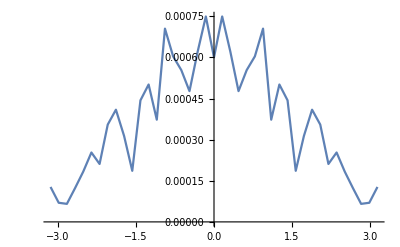

```mathematica
ListLinePlot[Transpose[pSpecSeriesX[[1,240]]],PlotRange->All]
```

### Hopf-AIC weight

```mathematica
?TBHopfAIC
```

TBHopfAIC[pSpec] fits the analytical forms for the Hopf and Fold bifurcation to the data in pSpec. 
It then outputs the AIC weight that corresponds to the Hopf fit. 
Note the Hopf fit is restricted such that S(ω_0)> 2 S(0). This stops the model being selected for the Fold spectrum.
pSpec = {freqVals,powerVals}
Outputs = hopfAICweight
AIC weights can be interpreted as the probability that the fitted model is the best model (in the AIC sense)

```mathematica
pSpecSeriesX//Dimensions
```

{100,240,2,41}

```mathematica
?TBHopfAIC
```

TBHopfAIC[pSpec] fits the analytical forms for the Hopf and Fold bifurcation to the data in pSpec. 
It then outputs the AIC weight that corresponds to the Hopf fit. 
Note the Hopf fit is restricted such that S(ω_0)> 2 S(0). This stops the model being selected for the Fold spectrum.
pSpec = {freqVals,powerVals}
Outputs = hopfAICweight
AIC weights can be interpreted as the probability that the fitted model is the best model (in the AIC sense)

```mathematica
Timing[TBHopfAIC[pSpecSeriesX[[1,160]]]]
```

{3.45961,4.29778×10^-8}

```mathematica
(*(* compute AIC weights - LONG SIMULATION *)
aicWeightSeriesX=Monitor[
Table[Quiet[TBHopfAIC[pSpecSeriesX[[i,j]]]],{i,1,numSims},{j,1,Dimensions[pSpecSeriesX]⟦2⟧}],
{ProgressIndicator[i,{1,numSims}],ProgressIndicator[j,{1,Dimensions[pSpecSeriesX]⟦2⟧}]}];*)
```

```mathematica
(*(* export aic weights to avoid simulating again *)
Export["../data_export/data_aic_stat.csv",aicWeightSeriesX];*)
```

```mathematica
(* import aic weight series *)
aicWeightSeriesX=Import["../data_export/data_aic_stat.csv"];
```

```mathematica
pSpecSeriesX//Dimensions
```

{100,240,2,41}

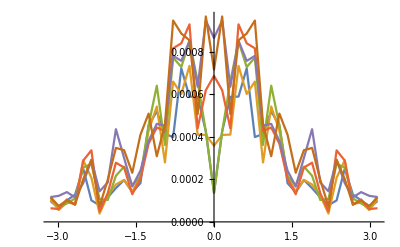

```mathematica
ListLinePlot[Table[Transpose[pSpecSeriesX[[1,t]]],{t,150,200,10}],PlotRange->All]
```

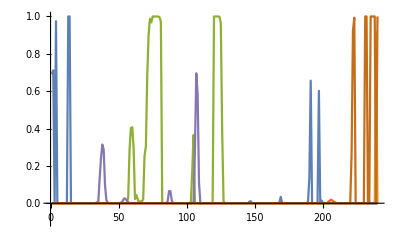

```mathematica
ListLinePlot[aicWeightSeriesX[[5;;10]],PlotRange->{-0.1,1}]
```

```mathematica
(* a plot averaged over simulations *)
meanAICSeriesX=Mean[aicWeightSeriesX];
devAICSeriesX=StandardDeviation[aicWeightSeriesX];
```

```mathematica
(* quantiles *)
quantile25aicWeightsX=Quantile[aicWeightSeriesX,0.25];
medianaicWeightsX=Quantile[aicWeightSeriesX,0.5];
quantile75aicWeightsX=Quantile[aicWeightSeriesX,0.75];
```

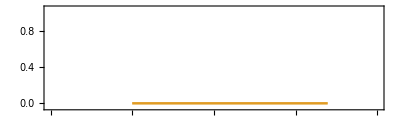

```mathematica
aicWeightSeriesPlotX=ListPlot[{{tValsShort[[windowComps+1;;]],quantile25aicWeightsX}ᵀ,
{tValsShort[[windowComps+1;;]],quantile75aicWeightsX}ᵀ,{tValsShort[[windowComps+1;;]],medianaicWeightsX}ᵀ},
Joined->True,
PlotStyle->{Lighter[TMBcolours⟦2⟧,0.5],Lighter[TMBcolours⟦2⟧,0.5],TMBcolours⟦2⟧},
Filling->{{2->{3}},{1->{3}}},
LabelStyle->14,
PlotRange->{{0,tmax},{-0.05,1.05}},
Frame->{{False,True},{True,True}},
FrameStyle->{{Automatic,TMBcolours[[2]]},{Automatic,Automatic}},
FrameLabel->{{"","w_AIC"},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicks->{{Automatic,All},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.3]
```

### Coherence factor

```mathematica
?TBCoherFactor
```

TBCoherFactor[{freqVals,powerVals}] computes the coherence factor of the given power specrum
output = coherenceFactor
Coherence factor is computed as CF=H/W where H is the height of the peak in spectrum and W is the relative width given by the width at half the height of the peak divided by the frequency that gives the peak

```mathematica
(* compute coherence factors *)
coherFactorSeriesX=Table[TBCoherFactor[pSpecSeriesX[[i,j]]],{i,1,numSims},{j,1,Dimensions[pSpecSeriesX]⟦2⟧}];
```

```mathematica
coherFactorSeriesX//Dimensions
```

{100,240}

```mathematica
(* a plot averaged over simulations *)
meanCoherSeriesX=Mean[coherFactorSeriesX];

devCoherSeriesX=StandardDeviation[coherFactorSeriesX];
```

```mathematica
(* quantiles *)
quantile25CoherX=Quantile[coherFactorSeriesX,0.25];
medianCoherX=Quantile[coherFactorSeriesX,0.5];
quantile75CoherX=Quantile[coherFactorSeriesX,0.75];
```

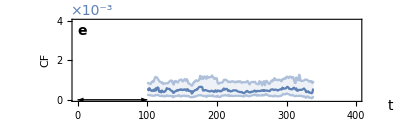

```mathematica
coherSeriesPlotX=ListPlot[{{tValsShort[[windowComps+1;;]],quantile25CoherX}ᵀ,
{tValsShort[[windowComps+1;;]],quantile75CoherX}ᵀ,
{tValsShort[[windowComps+1;;]],medianCoherX}ᵀ},
Joined->True,
PlotStyle->{Lighter[TMBcolours⟦1⟧,0.5],Lighter[TMBcolours⟦1⟧,0.5],TMBcolours⟦1⟧},
Filling->{{2->{3}},{1->{3}}},
LabelStyle->14,
Frame->{{True,False},{True,True}},
PlotRange->{{0,tmax},{0,0.004}},
FrameStyle->{{TMBcolours[[1]],Automatic},{Automatic,Automatic}},
FrameLabel->{{"CF",""},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicks->{{{{0,0},{0.001,1},{0.002,2},{0.003,3},{0.004,4}},Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0}],Scaled[{0,arHeight},{windowComps*dt2,0}]}],
Text[Style["×10^-3",14,TMBcolours[[1]]],indexPos],
Text[Style["t",14],Scaled[{1.1,-0.05}]],
Text[Style["e",14,Bold],Scaled[labelLetterPos]]}]
```

### Combine coherence factor and AIC weight

```mathematica
psdMetricPlotX=Overlay[{coherSeriesPlotX,aicWeightSeriesPlotX}]
```

-Graphics--Graphics-

## Bifurcation diagram

### Specifications

```mathematica
lt=0.0075; (* line thickness *)
ls=10; (* label size *)
ps=0.03; (* point size *)
imgs=400; (* image size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
plRange={{-1,0.5},{-1,1}}; (* plot range *)
(*frLabel={"μ","x"}; (* frame label *)*)
(*aRatio=2/3; (* aspect ratio *)*)

(* Colors of equilibrium lines in order as above *)
eqColors={Black,{Black,Dashing[{lt,3lt}]},Black,{Red,Dashing[{lt,3lt}]}};
```

### Output

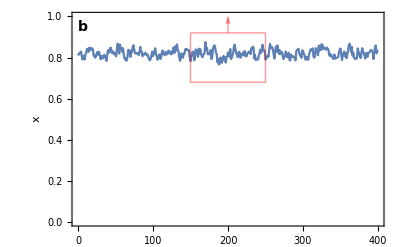

```mathematica
(* Incorporate with simulation and region of psd computation *)
lineStyle={Red,Opacity[0.4]};
sqHeight=0.12;
trajVal=0.8;

bifTrajX=Show[plotX,
PlotRange->{{0,tmax},{0,1}},
LabelStyle->14,
Frame->{{True,True},{True,True}},
AxesLabel->None,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
FrameLabel->{{"x",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
ImageSize->imgs,
Epilog->{Text[Style["b",14,Bold],Scaled[{0.035,0.93}]],
Directive[lineStyle],
Line[{{psdTime,trajVal-sqHeight},{psdTime,trajVal+sqHeight}}],
Line[{{psdTime-windowComps*dt2,trajVal-sqHeight},{psdTime-windowComps*dt2,trajVal+sqHeight}}],
Line[{{psdTime-windowComps*dt2,trajVal-sqHeight},{psdTime,trajVal-sqHeight}}],
Line[{{psdTime-windowComps*dt2,trajVal+sqHeight},{psdTime,trajVal+sqHeight}}],
Arrow[{{psdTime-windowComps*dt2/2,trajVal+sqHeight},{psdTime-windowComps*dt2/2,1}}]}
]
```

## Combined Plot

```mathematica
foldEwsPlot=Grid[{{psdAvHopfX},{bifTrajX},{varAvPlotX},{acAvPlotX},{psdMetricPlotX},{},{},{}},Spacings->{0,-0.6}]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics--Graphics-

```mathematica
Export["fold_harvest_stat_ews.png",foldEwsPlot,ImageResolution->200];
```